## Just Running α

```mathematica
data = {{18,0.9650167265225418, 0.017344747595112252},
{20,0.966466204711731, 0.020117004499406305},
{30,0.9704050688883262, 0.0315540914494925},
{40, 0.9711218590675714, 0.0391828439979559},
{50, 0.9718300071735966,0.04446350895038041 },
{60, 0.9718981425750751, 0.048258841913545666},
{70,0.9718928781450135,0.05111670000399582 },
{80,0.9716427871432295,0.053319787531834535  },
{90, 0.9712476054732628,0.0551433893476638 },
{100, 0.9713165853383029,0.05655666339443767 }
};
```

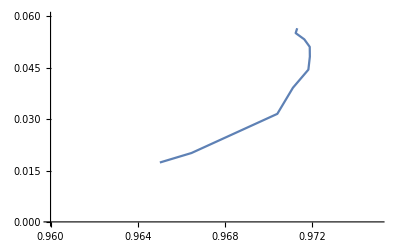

```mathematica
ListPlot[data[[;;,2;;3]],Joined->True,PlotRange->{{0.96,0.975},{0,0.06}}]
```

## Fitting with α and β with PS[k]

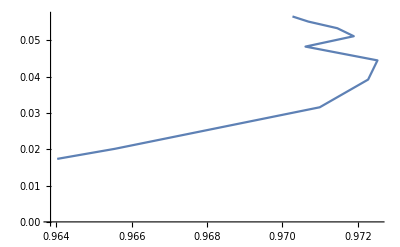

```mathematica
data2 = {
{18,0.9640234454042184,  0.017344747595112252},
{20,0.9655524283638014,0.020117004499406305  },
{30,0.9709893375132426,0.0315540914494925},
{40,0.9722734571343984, 0.0391828439979559},
{50, 0.9725212555958715, 0.04446350895038041},
{60,0.9706116187995583,0.04825997925772167 },
{70, 0.9718928781450135, 0.05111670000399582},
{80,0.9714554140053507, 0.053319787531834535},
{90,0.9706878093552394, 0.0551433893476638},
{100,0.9702662629254997, 0.05655666339443767}
}//ListPlot[#[[;;,2;;3]],Joined->True]&
```

## Fitting with α and β with PS[k/(k*)]

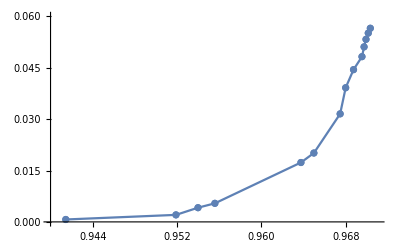

```mathematica
dataN60 = {{5,0.9414439302982188,0.0007040056187019992},
{7,0.9518930432557647,0.0020493125822198728},
{9, 0.953982784153641,0.004148606262751627},
{10,0.9555836992381092, 0.005421831996663472},
{18,0.9637430968768995,0.017344747595112252},
{20,0.9649725325537367,0.020117004499406305},
{30,0.967461024769543,0.0315540914494925 },
{40,0.967985239689709,0.0391828439979559},
{50,0.9687293705258315, 0.04446350895038041},
{60,0.9695309328760681, 0.04825997925772167},
{70,0.9697295179517035,0.05111670000399582 },
{80, 0.9699124732830823,0.053319787531834535 },
{90,0.9701272957630777, 0.0551433893476638},
{100, 0.9703236014156278, 0.05655666339443767}
};
ListPlot[dataN60[[;;,2;;3]],Joined->True,PlotRange->{{0.94,0.971},{0,0.06}},Mesh->Full]
```

{{5,0.93591,0.00121018},{7,0.940952,0.00336618},{9,0.945631,0.00654279},{20,0.957526,0.027834},{30,0.961156,0.0415979},{40,0.962519,0.0504692},{50,0.962394,0.0565006},{60,0.963111,0.0608712},{70,0.963242,0.0640887},{80,0.963179,0.0666273},{90,0.963467,0.0686057},{100,0.963731,0.0702315}}

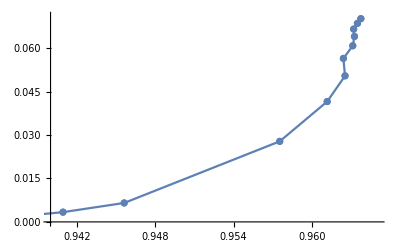

```mathematica
dataN50 = {
{5,0.935909688275167, 0.001210180278364914},
{7,0.94095197785514, 0.0033661761887858474},
{9,0.9456312032047436, 0.006542787494928124},
{20, 0.9575257154479674, 0.02783395924137185},
{30, 0.9611563395942724, 0.04159792549894576}, 
{40, 0.962519268640811, 0.050469195901686977},
{50,0.9623940404306319, 0.05650059068237701},
{60,0.9631109718011894, 0.06087121363008882}, 
{70, 0.963241523378533, 0.06408865809077244},
{80,0.9631793457087761, 0.06662733061977213},
{90, 0.9634673096824674, 0.06860567851597417},
{100,0.9637310123512761,0.0702315036241878}}
ListPlot[dataN50[[;;,2;;3]],Joined->True,PlotRange->{{0.94,0.965},{0,0.071}},Mesh->Full]
```

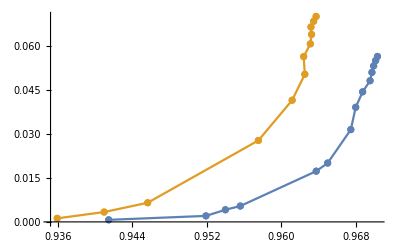

```mathematica
ListPlot[{dataN60[[;;,2;;3]], dataN50[[;;,2;;3]]}, Joined->True,Mesh->Full]
```

It was made a mistake according to the mass used

## Fitting r[k] and correcting N = 50

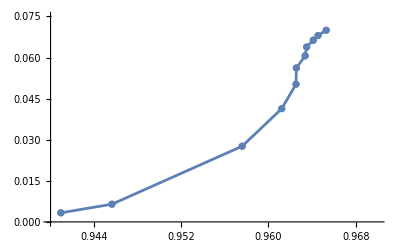

```mathematica
data50 = {
{7,0.94095197785514,0.00331251819397698 },
{9,0.9456312032047436,0.006455659656446529},
{20,0.9575884132915444,0.0276360243689275},
{30,0.9612144983538912, 0.041341755094031624},
{40,0.9625256047785742, 0.05025768026989949},
{50, 0.9625585570070614,0.05620768625560263},
{60,0.9633595260282624, 0.060616733162761574},
{70,0.9635048910994439,0.0638417385499708},
{80, 0.964108130573761, 0.06632991289425438},
{90,0.9645459066512111,0.06802903438045366},
{100,0.9652945235879725,0.06996216666354506}};
ListPlot[data50[[;;,2;;3]],Joined->True,PlotRange->{{0.94,0.97},{0,0.075}},Mesh->Full]
```

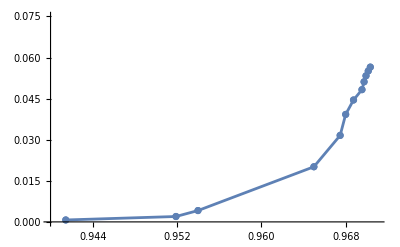

```mathematica
data60 = {
{5,0.9414439302982188, 0.0007040056187019992},
{7,0.9518930432557647,0.00196939911453734},
{9,0.953982784153641,0.0041435349950879625},
{20,0.9649725325537367, 0.02012730337896295},
{30,0.967461024769543, 0.03157119588903309},
{40,0.967985239689709,0.03924019998558403},
{50,0.9687293705258315,0.04450407707731335 },
{60,0.9695309328760681, 0.04828047238527404},
{70,0.9697295179517035, 0.05114009680396852},
{80,0.9699124732830823, 0.053332649597640294},
{90,0.9701272957630777,0.055098761124366506},
{100,0.9703236014156278,0.056512946303599404 }
};
ListPlot[data60[[;;,2;;3]],Joined->True,PlotRange->{{0.94,0.971},{0,0.075}},Mesh->Full]
```

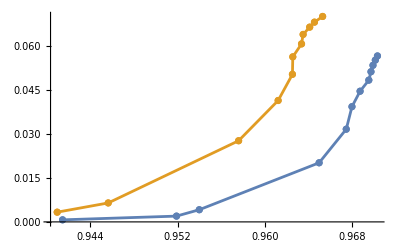

```mathematica
ListPlot[{data60[[;;,2;;3]], data50[[;;,2;;3]]}, Joined->True,Mesh->Full]
```